```mathematica
DSolve[{x'[t]==v1-v2*x[t]/sqrt[x[t]^2+y[t]^2],y'[t]==-y[t]*v2/sqrt[x[t]^2+y[t]^2]},{x,y},t]
```

```mathematica
DSolve[{x'[t]==v1-(v2 x[t])/sqrt[x[t]^2+y[t]^2],y'[t]==-(v2 y[t])/sqrt[x[t]^2+y[t]^2]},{x,y},t]
```

```mathematica
DSolve[{x'[t]==v-(w*x[t])/sqrt[x[t]^2+y[t]^2],y'[t]==-(w* y[t])/sqrt[x[t]^2+y[t]^2]},{x,y},t]
```

```mathematica
DSolve[{x'[t]==v-(w x[t])/sqrt[x[t]^2+y[t]^2],y'[t]==-(w y[t])/sqrt[x[t]^2+y[t]^2]},{x,y},t]
DSolve[{m*v'[t]==G-F-b*v[t],v[0]==0},v[t],t]
```

DSolve[{x'[t]==v-(w x[t])/sqrt[x[t]^2+y[t]^2],y'[t]==-(w y[t])/sqrt[x[t]^2+y[t]^2]},{x,y},t]

```mathematica
{{v[t]->-(ⅇ^(-(b t)/m) (-1+ⅇ^((b t)/m)) (F-G))/b}}
DSolve[{x'[t]==v-w*x[t]/sqrt[x[t]^2+y[t]^2],y'[t]==-y[t]*w/sqrt[x[t]^2+y[t]^2]},{x[t],y[t]},t]
```

{{v[t]→-(ⅇ^(-(b t)/m) (-1+ⅇ^((b t)/m)) (F-G))/b}}

```mathematica
DSolve[{x'[t]==v-(w x[t])/sqrt[x[t]^2+y[t]^2],y'[t]==-(w y[t])/sqrt[x[t]^2+y[t]^2]},{x[t],y[t]},t]
```

```mathematica
sol=DSolve[{x'[t]==v-(w x[t])/sqrt[x[t]^2+y[t]^2],y'[t]==-(w y[t])/sqrt[x[t]^2+y[t]^2]},{x[t],y[t]},t]
```

```mathematica
DSolve[{x'[t]==v-(w x[t])/sqrt[x[t]^2+y[t]^2],y'[t]==-(w y[t])/sqrt[x[t]^2+y[t]^2]},{x[t],y[t]},t]
sol=DSolve[{x'[y]==(x[y]-k*sqrt[x[y]^2+y^2])/y},x[y],y]
```

DSolve[{x'[t]==v-(w x[t])/sqrt[x[t]^2+y[t]^2],y'[t]==-(w y[t])/sqrt[x[t]^2+y[t]^2]},{x[t],y[t]},t]

```mathematica
DSolve[{x'[y]==(-k Sqrt[y^2+x[y]^2]+x[y])/y,x[-d]==0},x[y],y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
{{x[y]->y Sinh[k Log[-d]-k Log[y]]}}
sol=DSolve[{x'[t]==v1-(v2 x[t])/Sqrt[x[t]^2+y[t]^2],y'[t]==-(v2 y[t])/Sqrt[x[t]^2+y[t]^2],x[0]==0,y[0]==-d},{x[t],y[t]},t]
```

{{x[y]→y Sinh[k Log[-d]-k Log[y]]}}

DSolve::deqn: Equation or list of equations expected instead of True in the first argument SuperscriptBox[SuperscriptBox[TrueTrue.

```mathematica
DSolve[{x'[t]==v1-(v2 x[t])/(√(x[t]^2+y[t]^2)),y'[t]==-(v2 y[t])/(√(x[t]^2+y[t]^2)),True,True},{x[t],y[t]},t]
sol=DSolve[{x'[t]==v1-(v2 x[t])/Sqrt[x[t]^2+y[t]^2],y'[t]==-(v2 y[t])/Sqrt[x[t]^2+y[t]^2]},{x[0]==0,y[0]==-d},{x[t],y[t]},t]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument SuperscriptBox[SuperscriptBox[TrueTrue.

DSolve[{x'[t]==v1-(v2 x[t])/(√(x[t]^2+y[t]^2)),y'[t]==-(v2 y[t])/(√(x[t]^2+y[t]^2)),True,True},{x[t],y[t]},t]

DSolve::dsvar: {x[t], y[t]} cannot be used as a variable.

```mathematica
DSolve[{x'[t]==v1-(v2 x[t])/(√(x[t]^2+y[t]^2)),y'[t]==-(v2 y[t])/(√(x[t]^2+y[t]^2))},{True,True},{x[t],y[t]},t]
Plot[y *Sinh[2Log[-100]-2 Log[y]],{y,-100,0}]
```

DSolve::dsvar: {x[t], y[t]} cannot be used as a variable.

DSolve[{x'[t]==v1-(v2 x[t])/(√(x[t]^2+y[t]^2)),y'[t]==-(v2 y[t])/(√(x[t]^2+y[t]^2))},{True,True},{x[t],y[t]},t]

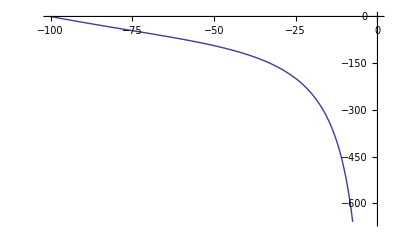
```mathematica
-Graphics-
Plot[y *Sinh[0.5*Log[-100]-2 Log[y]],{y,-100,0}]
```

-Graphics-

-Graphics-

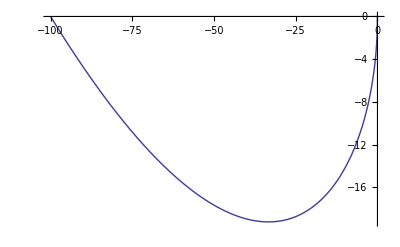

```mathematica
-Graphics-
Plot[{y Sinh[0.5 Log[-100]-0.5 Log[y]]},{y,-100,0}]
```

```mathematica
DSolve[{x'[y]==(-k Sqrt[y^2+x[y]^2]+x[y])/y},x[y],y]
```

{{x[y]→y Sinh[C[1]-k Log[y]]}}

```mathematica
DSolve[{x'[y]==(-k Sqrt[y^2+x[y]^2]+x[y])/y,x[-d]==0},x[y],y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
{{x[y]->y Sinh[k Log[-d]-k Log[y]]}}
Plot[{y Sinh[0.5 Log[-100]-0.5 Log[y]]},{y,-100,0}]
```

```mathematica
{{x[y]->y Sinh[k Log[y]-k Log[-d]]}}
```

{{x[y]→-y Sinh[k Log[-d]-k Log[y]]}}

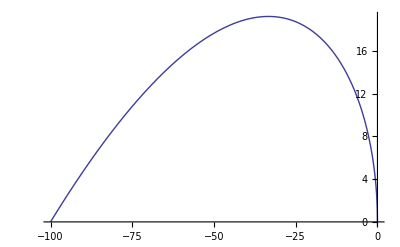

```mathematica
{{x[y]->-y Sinh[k Log[-d]-k Log[y]]}}
Plot[{y Sinh[0.5 Log[y]-0.5 Log[-100]]},{y,-100,0}]
```